Predator-Prey Relationships with Edible Habitat Complexity in Benthic Communities

Eden Forbes, 2025

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
Quiet[<<"/Users/eden/Desktop/RESEARCH/CODE/Dynamica/Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## Building Block Visualizers

```mathematica
T2[x_]:=(595/(30+ x));
```

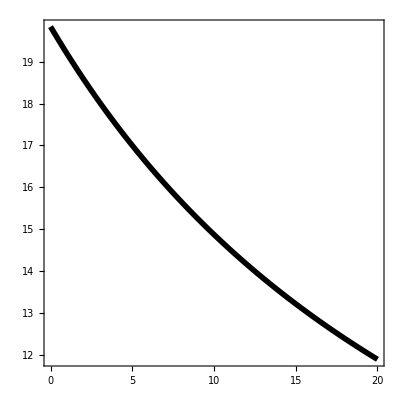

```mathematica
Plot[T2[x],{x,0,20},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,All},Frame->True,LabelStyle->{Black,20},AspectRatio->1
]
```

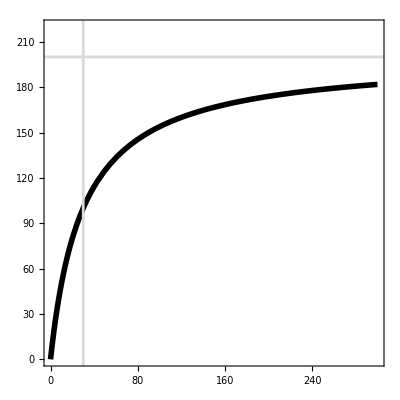

```mathematica
Plot[T2[x]*x,{x,0,300},PlotStyle->{Black,Thickness[0.01]},PlotRange->{All,{0,220}},Frame->True,LabelStyle->{Black,20},AspectRatio->1,GridLines->{{30},{200}}, GridLinesStyle->Thickness[0.005]
]
```

```mathematica
β[rat_,steep_]:= (rat)^steep/((rat)^steep+α^steep); (* When the ratio is 10:1 (1),  start eating Dreissena *)
```

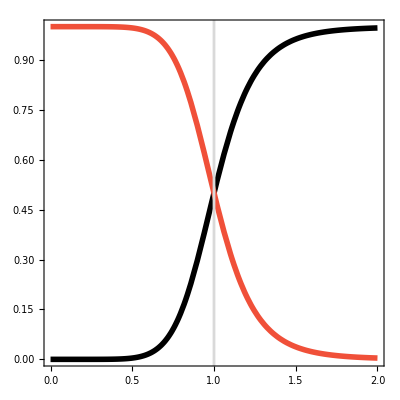

```mathematica
Show[
Plot[β[x,8]/.{α->1},{x,0,2},PlotStyle->{Black,Thickness[0.01]},PlotRange->All],
(*Plot[β[x,1]/.{α->1},{x,0,2},PlotStyle->{Black,Dashed,Thickness[0.01]},PlotRange->All],*)
Plot[1-β[x,8]/.{α->1},{x,0,2},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]},PlotRange->All],
(*Plot[1-β[x,1]/.{α->1},{x,0,2},PlotStyle->{Blue,Dashed,Thickness[0.01]},PlotRange->All],*)
Frame->True,LabelStyle->{Black,20},AspectRatio->1,AxesOrigin->{0,0},GridLines->{{1},{}}, GridLinesStyle->Thickness[0.005]
]
```

## Predator-Prey Subsystem

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,yj,fjp,δ]
```

```mathematica
PP = DynamicalSystem[{
r*V*(1 - V/kv)-(fvp/(hvp+ V))*V*P - dv V,
((yv ep)/yp)*(fvp/(hvp+ V))*V*P - dp*P
},
{{V,-0.01,10000},{P,-0.01,1000}},
{{r,0,100},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0,1},{hvp,0,1},{fvp,0,1},{dp,0.001,0.08},{yp,0,10000},
{kv,1,1000}
}];
PP = PP/.{r->0.1,kv->1000,dv->1/30, yv->0.67,ep->0.8,hvp->30, fvp->0.08*4900/0.67,dp->0.04, yp->4900};
```

```mathematica
PPBD = DisplayBifurcationDiagram[PP,dp,MinStepSize->0.1,MaxSteps->100000]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,dp}={666.667,0,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,dp}={666.667,0,0.08}

-Graphics3D-

{BifurcationPoint[Branch,{0,0},{dp→0,dv→1/30,ep→0.8,fvp→585.075,hvp→30,kv→1000,r→0.1,yp→4900,yv→0.67}],BifurcationPoint[Hopf,{318.333333333333,0.0207385700113379},{dp→0.058488038277512,dv→1/30,ep→0.8,fvp→585.075,hvp→30,kv→1000,r→0.1,yp→4900,yv→0.67}]}

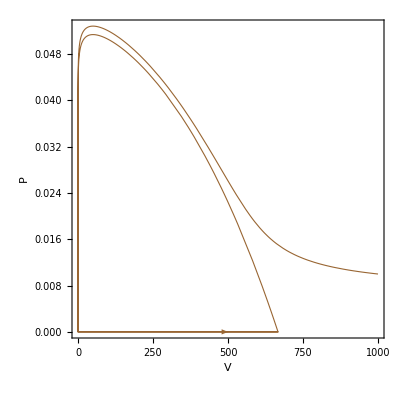

```mathematica
DisplayTrajectories[PP,{{1000,0.01}},2000,PlotRange->All,MaxStepSize->0.1,MaxSteps->Infinity]
```

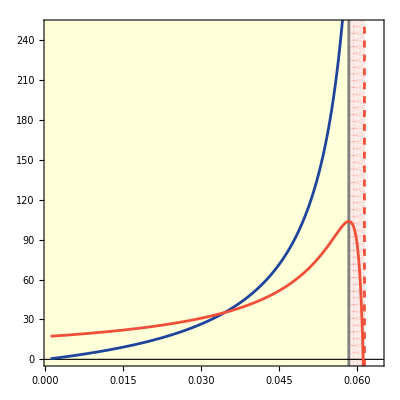

```mathematica
Show[
RegionPlot[0.0615 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.058488 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

ListPlot[PPBD[[1]][[1]][[3]][[3]][[1]][[All,{1,2}]],Joined->True,PlotStyle->RGBColor["#1F449C"]],
ListPlot[MapThread[List,{PPBD[[1]][[1]][[3]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[3]][[3]][[1]][[All,3]]*5000}],Joined->True,PlotStyle->RGBColor["#F05039"]],

ListPlot[PPBD[[1]][[1]][[4]][[3]][[1]][[All,{1,2}]],Joined->True,PlotStyle->RGBColor["#1F449C"]],

ListPlot[MapThread[List,{PPBD[[1]][[1]][[4]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[4]][[3]][[1]][[All,3]]*5000}],Joined->True,PlotStyle->RGBColor["#F05039"],Frame->True,FrameTicks->{{None,All},{All,None}},FrameTicksStyle->{{None,RGBColor["#F05039"]},{Black,None}},LabelStyle->18],


Frame->True,FrameTicks->{{All,{{0,"0"},{100,"1"},{200,"2"},{300,"3"},{400,"4"},{500,"5"}}},{All,None}},FrameTicksStyle->{{RGBColor["#1F449C"],RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{0,250}}]
```

```mathematica
dV = r*V*(1 - V/kv)-(fvp/(hvp+ V))*V*P - dv V;
dP = ((yv ep)/yp)*(fvp/(hvp+ V))*V*P - dp*P;
```

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
```

```mathematica
JM = {{J11,J12},{J21,J22}};
JM//MatrixForm
```

(-dv+r-(2 r V)/kv-(fvp hvp P)/(hvp+V)^2 | -(fvp V)/(hvp+V)
(ep fvp hvp P yv)/((hvp+V)^2 yp) | -dp+(ep fvp V yv)/((hvp+V) yp))

#### Feedback Level 1

```mathematica
L1 = J11+J22;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22);
```

### CHART

```mathematica
solsPP= Solve[{dV==0,dP==0},{V,P}];
```

```mathematica
solsPP
```

{{V→0,P→0},{V→(-dv kv+kv r)/r,P→0},{V→-(dp hvp yp)/(dp yp-ep fvp yv),P→-(ep hvp yv (-dp dv kv yp+dp hvp r yp+dp kv r yp+dv ep fvp kv yv-ep fvp kv r yv))/(kv (dp yp-ep fvp yv)^2)}}

```mathematica
Vp = solsPP[[2,1,2]];
Vo = solsPP[[3,1,2]];
Po = solsPP[[3,2,2]];
P0=(((yv ep)/yp)*((fvp *Vp)/(hvp^2+ Vp^2))*Vp)/dp;
```

```mathematica
IFIT = FullSimplify[dV/V]
```

-dv+r-(r V)/kv-(fvp P)/(hvp+V)

```mathematica
r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;
```

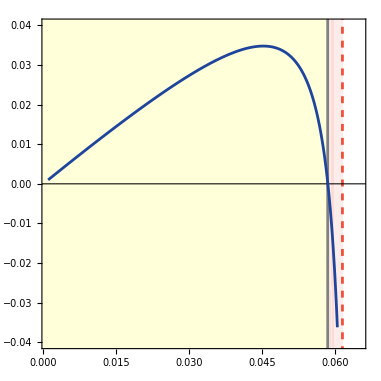

```mathematica
Show[
RegionPlot[0.0615 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.058488 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[IFIT/.{V->Vo,P->Po},{dp,0.001,0.0638}, PlotStyle->RGBColor["#1F449C"]],


Frame->True,
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-0.04,0.04}}]
```

```mathematica
IDD = FullSimplify[D[dV/V,V]];
```

```mathematica
IDD
```

-r/kv+(fvp P)/(hvp+V)^2

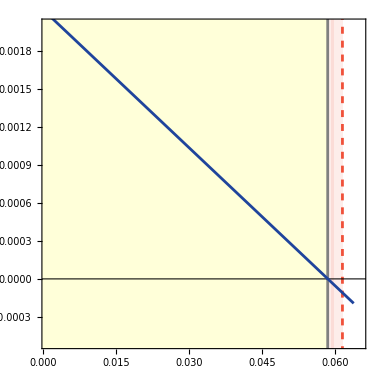

```mathematica
Show[
RegionPlot[0.0615 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.058488 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[IDD/.{V->Vo,P->Po},{dp,0.001,0.0638}, PlotStyle->RGBColor["#1F449C"]],


Frame->True,
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-0.0005,0.002}}]
```

```mathematica
Solve[P0==1,dp]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{dp→0.0638707}}

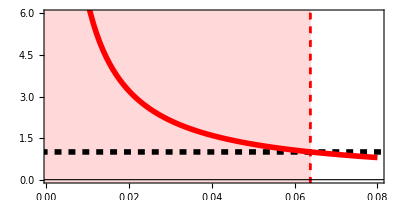

```mathematica
Show[
RegionPlot[0.0638 > x>-1,{x,-1,0.14},{y,-1,20}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->LightRed],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[x=1,{x,-1,0.14},PlotStyle->{Black,Dashed, Thickness[0.01]}],
Plot[P0,{dp,0.001,0.08},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Frame->True,LabelStyle->{Black,16},AspectRatio->1/2,PlotRange->{{0.001,0.08},{0,6}}
]
```

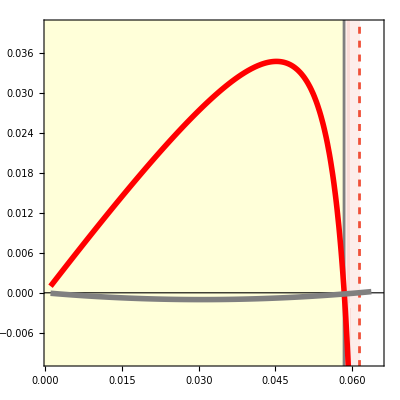

```mathematica
Show[
RegionPlot[0.0615 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.058488 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[L1/.{V->Vo,P->Po},{dp,0.001,0.0638},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L2/.{V->Vo,P->Po},{dp,0.001,0.0638},PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-0.01,0.04}}]
```

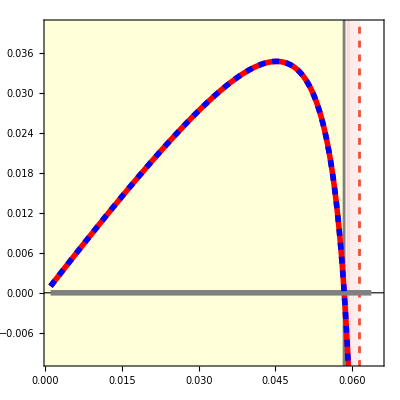

```mathematica
Show[
RegionPlot[0.0615 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.058488 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[J11/.{V->Vo,P->Po},{dp,0.001,0.0638},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[J22/.{V->Vo,P->Po},{dp,0.001,0.0638},PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[L1/.{V->Vo,P->Po},{dp,0.001,0.0638},PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-0.01,0.04}}]
```

### Sims

```mathematica
min = 0.01; max =0.058; gran = 0.001;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[PP/.{dp->i*gran},{{1000,0.01}},5000,PlotRange->All,MaxStepSize->0.1,MaxSteps->Infinity];
(* Simulation *)
DisplayTrajectories[PP/.{dp->i*gran},{Last[First[$Trajectories]]},100000, MaxStepSize->0.01,MaxSteps->Infinity, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
]
```

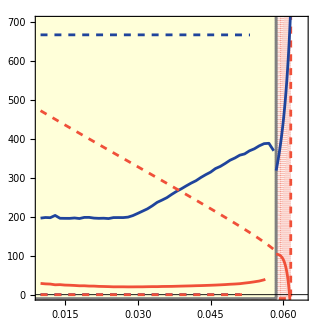

```mathematica
Show[
RegionPlot[0.0615 > x>-1,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.058488 > x,{x,-1,0.14},{y,-10,1000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

ListPlot[PPBD[[1]][[1]][[1]][[3]][[1]][[All,{1,2}]],Joined->True,PlotStyle->RGBColor["#1F449C"]],
ListPlot[MapThread[List,{PPBD[[1]][[1]][[1]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[1]][[3]][[1]][[All,3]]*5000}],Joined->True,PlotStyle->RGBColor["#F05039"]],

(*ListPlot[PPBD[[1]][[1]][[2]][[3]][[1]][[All,{1,2}]],Joined->True,PlotStyle->RGBColor["#1F449C"]],

ListPlot[MapThread[List,{PPBD[[1]][[1]][[2]][[3]][[1]][[All,1]],PPBD[[1]][[1]][[2]][[3]][[1]][[All,3]]*5000}],Joined->True,PlotStyle->RGBColor["#F05039"],Frame->True,FrameTicks->{{None,All},{All,None}},FrameTicksStyle->{{None,RGBColor["#F05039"]},{Black,None}},LabelStyle->18],
*)

ListPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"]}],
ListPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*5000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*5000}],Joined->True, PlotStyle->{RGBColor["#F05039"]}],
ListPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*5000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0.01,0.064},{0,700}}]
```

```mathematica
Vpeaks
```

{{0.01,666.666},{0.011,666.666},{0.012,666.666},{0.013,666.666},{0.014,666.666},{0.015,666.666},{0.016,666.666},{0.017,666.666},{0.018,666.666},{0.019,666.666},{0.02,666.665},{0.021,666.665},{0.022,666.665},{0.023,666.665},{0.024,666.665},{0.025,666.665},{0.026,666.664},{0.027,666.664},{0.028,666.664},{0.029,666.664},{0.03,666.663},{0.031,666.663},{0.032,666.662},{0.033,666.662},{0.034,666.661},{0.035,666.66},{0.036,666.659},{0.037,666.658},{0.038,666.657},{0.039,666.655},{0.04,666.653},{0.041,666.651},{0.042,666.648},{0.043,666.644},{0.044,666.639},{0.045,666.633},{0.046,666.626},{0.047,666.616},{0.048,666.603},{0.049,666.586},{0.05,666.563},{0.051,666.529},{0.052,666.481},{0.053,666.407},{0.054,666.287},{0.055,666.072},{0.056,665.619},{0.057,664.246},{0.058,634.915}}

```mathematica
Pmeans[[All]][[-1]]
```

{0.058,0.0122903}

## Combined (D Growth)

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
β[V_,Z_]:= (V/Z)^ω/((V/Z)^ω+α^ω);
```

```mathematica
FULL = DynamicalSystem[{
r*(1+δ M/kz)*V*(1 - V/(kv*(1+δ M/kz)))-((fvp β[V,M])/(hvp+ V))*V*P - dv V,
((yv ep)/yp)*((fvp β[V,M])/(hvp+ V))*V*P - dp*P,
b M (1-J/kz)-g J - dj J,
g J (1-M/kz)- dm M
},
{{V,-0.01,10000},{P,-0.01,100}, {J,-0.01,10000},{M,-0.01,10000}},
{{r,0,100},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0,1},{hvp,0,1},{fvp,0,1},{dp,0.0001,0.08},{yp,0,10000},
{α,0.001,1},{ω,1,4},{δ,0,4},
{b,0.0001,2000},{g,0.0001,1000},{kz,0.001,100},{kv,1,2000},{dj,0.0001,1},{dm,0.0001,1}
}]
FULL = FULL/.{b->1370,g->1/270,dj->1/365,dm->1/1460,r->0.1,kz->200,kv->1000,dv->1/30, yv->0.67,ep->0.8,hvp->30, fvp->0.08*4900/0.67,dp->0.04, yp->4900,α->1,ω->4,δ->2};
```

DynamicalSystem[«4 ODEs»,{V,P,J,M},{r,dv,yv,ep,hvp,fvp,dp,yp,α,ω,δ,b,g,kz,kv,dj,dm}]

```mathematica
DisplayPhasePortrait[FULL/.{kz->1000},Tries->1000,PlotRange->All]
$PhasePortraitEPs
```

General::munfl: 1.99344×10^-205 1.99344×10^-205 is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression 1/0. encountered.

General::munfl: 1/((9.90905×10^215)^2) is too small to represent as a normalized machine number; precision may be lost.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::munfl: 1.99344×10^-205 1.99344×10^-205 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigensystem::mindet: Input matrix contains an indeterminate entry.

MapThread::list: List expected at position 2 in MapThread[{#1,#2}&,Eigensystem[{{Indeterminate,-559.88,0,Indeterminate},{Indeterminate,0.021244,0,Indeterminate},{0,0,-0.00644343,1370.},{0,0,0.0037037,-0.000684932}}]].

Part::partw: Part 2 of {#1,#2}& does not exist.

Part::partw: Part 2 of Eigensystem[{{Indeterminate,-559.88,0,Indeterminate},{Indeterminate,0.021244,0,Indeterminate},{0,0,-0.00644343,1370.},{0,0,0.0037037,-0.000684932}}] does not exist.

MapThread::list: List expected at position 2 in MapThread[({#1,#2}&)⟦2⟧,Eigensystem[{{Indeterminate,-559.88,0,Indeterminate},{Indeterminate,0.021244,0,Indeterminate},{0,0,-0.00644343,1370.},{0,0,0.0037037,-0.000684932}}]⟦2⟧].

-Graphics3D-

{EquilibriumPoint[Saddle,Node,{0,0,999.994,843.93}],EquilibriumPoint[Saddle,Node,{0,0,0,0}],EquilibriumPoint[Saddle,Mixed,{50.,0.00843197,0,0}],EquilibriumPoint[Saddle,Mixed,{666.667,0,0,0}],EquilibriumPoint[Stable,Mixed,{978.9,0.368254,999.994,843.93}],EquilibriumPoint[Saddle,Node,{2354.53,0,999.994,843.93}]}

```mathematica
DisplayBifurcationDiagram[FULL,dp,StateVariables->{V,P}, MaxSteps->Infinity, MinStepSize->0.1]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={0,0,199.999,168.786,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={2354.53,0,199.999,168.786,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,dp}={2354.53,0,199.999,168.786,0.08}

-Graphics3D-

{BifurcationPoint[Branch,{0,0,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0,dv→1/30,ep→0.8,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}],BifurcationPoint[Hopf,{241.044445473069,0.121448995015539,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.0458849719983695,dv→1/30,ep→0.8,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}],BifurcationPoint[Hopf,{1161.17067518634,0.243067289257838,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.0623603002924397,dv→1/30,ep→0.8,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→4}]}

#### Funcs

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; α=1; ω=4; δ=2; dp = 0.04;
```

```mathematica
TS=NDSolveValue[
{ V'[t]==r*V[t]*(1 - V[t]/kv)-(fvp/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*(fvp/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],

V[0]==1000,P[0]==1
},{V,P},{t,0,10000}];
TS2=NDSolveValue[
{ V'[t]==r*(1+δ M[t]/kz)*V[t]*(1 - V[t]/(kv*(1+δ M[t]/kz)))-((fvp β[V[t],M[t]])/(hvp+ V[t]))*V[t]*P[t] - dv V[t],
P'[t]==((yv ep)/yp)*((fvp β[V[t],M[t]])/(hvp+ V[t]))*V[t]*P[t] - dp*P[t],
J'[t]==b M[t](1-J[t]/kz) -g J[t] - dj J[t],
M'[t]==g J[t](1-M[t]/kz)- dm M[t],

V[0]==680,P[0]==0.5,J[0]==50, M[0]==50, 
WhenEvent[t==5500,{V[t]->680,P[t]->0.000008,J[t]->1,M[t]->1}]
},{V,P,J,M},{t,0,10000}];
```

NDSolveValue::ndsz: At t == 599.812, step size is effectively zero; singularity or stiff system suspected.

#### Plots

InterpolatingFunction::dmval: Input value {2500.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

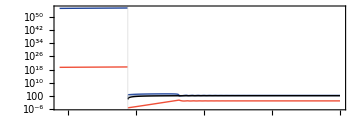

```mathematica
Show[
LogPlot[Evaluate[#[t]& /@TS],{t,2500,5500},PlotRange->All,ImageSize->Medium,
 PlotStyle->{{RGBColor["#1F449C"],Thick},{RGBColor["#F05039"],Thick},{RGBColor["#A8B6CC"],Thick},{Black,Thick}},
PlotPoints->500],
LogPlot[Evaluate[#[t]& /@TS2],{t,5500,8000},PlotRange->All,ImageSize->Medium,
 PlotStyle->{{RGBColor["#1F449C"],Thick},{RGBColor["#F05039"],Thick},{RGBColor["#A8B6CC"],Thick},{Black,Thick}},
PlotPoints->500],
TicksStyle->10,AxesOrigin->{2500,-20},
AspectRatio->1/3, LabelStyle->16, Frame->True,  FrameStyle->Black,
GridLines->{{5500},{}},GridLinesStyle->{Dashed,Thick}
]
```

## PCHART

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
dV = r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+ V))*V*P - dv V;
dP = ((yv ep)/yp)*((fvp β[V,M])/(hvp+ V))*V*P - dp*P ;
dJ = b M (1-J/kz)-g J - dj J;
dM = g J (1-M/kz)- dm M;
```

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J13 = FullSimplify[D[dV,J]];
J14 = FullSimplify[D[dV,M]];
```

```mathematica
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
J23 = FullSimplify[D[dP,J]];
J24 = FullSimplify[D[dP,M]];
```

```mathematica
J31 = FullSimplify[D[dJ,V]];
J32 = FullSimplify[D[dJ,P]];
J33 = FullSimplify[D[dJ,J]];
J34 = FullSimplify[D[dJ,M]];
```

```mathematica
J41 = FullSimplify[D[dM,V]];
J42 = FullSimplify[D[dM,P]];
J43 = FullSimplify[D[dM,J]];
J44 = FullSimplify[D[dM,M]];
```

```mathematica
JM = {{J11,J12,J13,J14},{J21,J22,J23,J24},{J31,J32,J33,J34},{J41,J42,J43,J44}};
JM//MatrixForm
```

(-dv+r (1-(2 V)/kv+(M δ)/kz)-(fvp P (V/M)^ω (hvp (V/M)^ω+α^ω (hvp+(hvp+V) ω)))/((hvp+V)^2 ((V/M)^ω+α^ω)^2) | -(fvp V (V/M)^ω)/((hvp+V) ((V/M)^ω+α^ω)) | 0 | (V (hvp M r ((V/M)^ω+α^ω)^2 δ+M r V ((V/M)^ω+α^ω)^2 δ+fvp kz P (V/M)^ω α^ω ω))/(kz M (hvp+V) ((V/M)^ω+α^ω)^2)
(ep fvp P (V/M)^ω yv (hvp (V/M)^ω+α^ω (hvp+(hvp+V) ω)))/((hvp+V)^2 yp ((V/M)^ω+α^ω)^2) | -dp+(ep fvp V (V/M)^ω yv)/((hvp+V) yp ((V/M)^ω+α^ω)) | 0 | -(ep fvp P V yv ω Sech[1/2 ω (Log[V/M]-Log[α])]^2)/(4 hvp M yp+4 M V yp)
0 | 0 | -((dj+g) kz+b M)/kz | b-(b J)/kz
0 | 0 | g-(g M)/kz | -(g J+dm kz)/kz)

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jVV,jVP,0,jVM},{jPV,jPP,0,jPM},{0,0,jJJ,jJM},{0,0,jMJ,jMM}};
DJac//MatrixForm
```

(jVV | jVP | 0 | jVM
jPV | jPP | 0 | jPM
0 | 0 | jJJ | jJM
0 | 0 | jMJ | jMM)

```mathematica
Expand[CharacteristicPolynomial[DJac,x]]
```

jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJM jMJ jPP jVV+jJJ jMM jPP jVV+jJM jMJ jPP x-jJJ jMM jPP x+jJJ jPV jVP x+jMM jPV jVP x+jJM jMJ jVV x-jJJ jMM jVV x-jJJ jPP jVV x-jMM jPP jVV x-jJM jMJ x^2+jJJ jMM x^2+jJJ jPP x^2+jMM jPP x^2-jPV jVP x^2+jJJ jVV x^2+jMM jVV x^2+jPP jVV x^2-jJJ x^3-jMM x^3-jPP x^3-jVV x^3+x^4

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jJJ+jMM+jPP+jVV

```mathematica
L1 = J11+J22+J33+J44;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22)+(J43*J34-J33*J44)+(-J11*J44)+(-J11*J33)+(-J22*J44)+(-J22*J33);
```

#### Feedback Level 3

```mathematica
L3 = -(J34 J43 J22 -J33 J44 J22 + J33 J21 J12 + J44 J21 J12 + J34 J43 J11 - J33 J44 J11 - J33 J22 J11 - J44 J22 J11);
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJM jMJ jPP jVV+jJJ jMM jPP jVV

```mathematica
L4 =-(J34 J43 J12 J21-J33 J44 J12 J21-J34 J43 J22 J11+J11 J22 J33 J44);
```

#### Oscillation Criterion

```mathematica
OC = ((L1*L2+L3)*L3)/L1^2-L4;
```

### CHART - dp

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; α=1; ω=4; δ=2;
```

```mathematica
solsPP= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

$Aborted

```mathematica
solsPP[[7]]/.dp->0.06
```

{V→534.297,P→0.177307,J→199.999,M→168.786}

```mathematica
Vp = Re[solsPP[[3,1,2]]];
Jp = Re[solsPP[[3,3,2]]];
Mp = Re[solsPP[[3,4,2]]];

Vo = Re[solsPP[[7,1,2]]];
Po = Re[solsPP[[7,2,2]]];
Jo = Re[solsPP[[7,3,2]]];
Mo = Re[solsPP[[7,4,2]]];

P0=(((yv ep)/yp)*((fvp β[Vp,Mp])/(hvp+ Vp))*Vp)/dp;
```

```mathematica
FindRoot[P0==1,{dp,0.065}]
```

{dp→0.0631931}

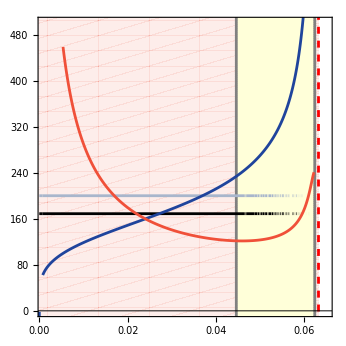

```mathematica
Show[
RegionPlot[0.06319> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.06236 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[Jo,{dp,0.00,0.06217},PlotStyle->RGBColor["#A8B6CC"], PlotPoints->400],
Plot[Mo,{dp,0.00,0.06217},PlotStyle->Black, PlotPoints->400],
Plot[Vo,{dp,0.00,0.06217},PlotStyle->RGBColor["#1F449C"], PlotPoints->400],
Plot[Po*1000,{dp,0.00,0.06217},PlotStyle->RGBColor["#F05039"], PlotPoints->400],

Frame->True,FrameTicks->{{All,{{0,"0"},{100,"0.1"},{200,"0.2"},{300,"0.3"},{400,"0.4"},{500,"0.5"}}},{All,None}},FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{0,500}}]
```

```mathematica
IFIT = FullSimplify[dV/V]
```

-dv+r-(r V)/kv-(fvp P (V/M)^ω)/((hvp+V) ((V/M)^ω+α^ω))+(M r δ)/kz

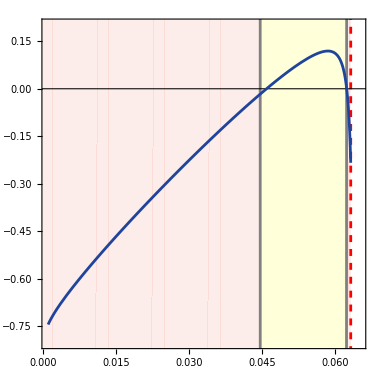

```mathematica
Show[
RegionPlot[0.06319> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.06236 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[IFIT/.{V->Vo,P->Po, J->Jo, M->Mo},{dp,0.001,0.06319}, PlotStyle->RGBColor["#1F449C"]],


Frame->True,
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-0.8,0.2}}]
```

```mathematica
IDD = FullSimplify[D[dV/V,V]]
```

-r/kv+(fvp P (V/M)^ω (V (V/M)^ω+α^ω (V-(hvp+V) ω)))/(V (hvp+V)^2 ((V/M)^ω+α^ω)^2)

```mathematica
FullSimplify[D[(V/Z)^ω/((V/Z)^ω+α^ω),V]]
```

((V/Z)^ω α^ω ω)/(V ((V/Z)^ω+α^ω)^2)

```mathematica
Show[
RegionPlot[0.06319> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.06236 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[IDD/.{V->Vo,P->Po, J->Jo, M->Mo},{dp,0.001,0.06319}, PlotStyle->RGBColor["#1F449C"]],


Frame->True,
LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-0.002,0.001}}]
```

-Graphics-

#### Loops kz = 200

```mathematica
Show[
RegionPlot[0.064 > x>-1,{x,-1,0.14},{y,-1,20}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->LightRed],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],
Plot[x=1,{x,-1,0.14},PlotStyle->{Black,Dashed, Thickness[0.01]}],
Plot[P0,{dp,0.001,0.08},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Frame->True,LabelStyle->{Black,16},AspectRatio->1/2,PlotRange->{{0.001,0.08},{0,6}}
]
```

-Graphics-

```mathematica
Quiet[FindRoot[(OC/.{V->Vo,P->Po,J->Jo,M->Mo})==0,{dp,0.03}]]
Quiet[FindRoot[(OC/.{V->Vo,P->Po,J->Jo,M->Mo})==0,{dp,0.0638}]]
```

{dp→0.045885}

{dp→0.0623603}

```mathematica
Show[
RegionPlot[0.06319> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.06236 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[((L1*L2+L3)*L3)/L1^2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0635},PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[L4/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0635},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[OC/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0635},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],


Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-8,1}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.06319> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.06236 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
Plot[OC/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0635},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],

Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-50,180}}]
```

-Graphics-

```mathematica
(J12*J21-J11*J22)+(J13*J31-J11*J33)+(-J11*J44)+(-J11*J33)+(-J22*J44)+(-J22*J33);
```

```mathematica
Show[
RegionPlot[0.06319> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.06236 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

(*Plot[(J12*J21-J11*J22)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(J13*J31-J11*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J11*J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],*)
Plot[(-J11*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],
(*Plot[(-J22*J44)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
Plot[(-J22*J33)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Gray,Thickness->0.01},PlotPoints->100],
*)
Plot[L2/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-50,180}}]
```

-Graphics-

```mathematica
Show[
RegionPlot[0.06319> x>-1,{x,-1,0.14},{y,-100,2500}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.06236 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
Plot[x=0,{x,-1,0.14},PlotStyle->{Black,Thickness[0.002]}],

Plot[(J11)/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Red,Thickness->0.01},PlotPoints->100],

Plot[-J11*J33/.{V->Vo,P->Po,J->Jo,M->Mo},{dp,0.001,0.0639},
PlotStyle->{Blue,Dashed,Thickness->0.01},PlotPoints->100],
Frame->True,LabelStyle->{Black,16},AspectRatio->1,PlotRange->{{0.001,0.065},{-1,1}}]
```

-Graphics-

### CHART - kz

```mathematica
Clear[kz]
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;dp=0.04; α=1; ω=4; δ=2;
```

```mathematica
solsKZ= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsKZ[[7]]/.kz->100
```

{V→,P→0.0714522,J→99.9994,M→84.393}

```mathematica
Vp = Re[solsKZ[[4,1,2]]];
Jp = Re[solsKZ[[4,3,2]]];
Mp = Re[solsKZ[[4,4,2]]];

Vo = Re[solsKZ[[7,1,2]]];
Po = Re[solsKZ[[7,2,2]]];
Jo = Re[solsKZ[[7,3,2]]];
Mo = Re[solsKZ[[7,4,2]]];

P0=(((yv ep)/yp)*((fvp β[Vp,Mp])/(hvp+ Vp))*Vp)/dp;
```

```mathematica
Reduce[P0==1,kz]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Re[kz]==-2434.61||Re[kz]==2434.61

```mathematica
Show[
LogPlot[x=0,{x,-1,3100},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[x>78,{x,-100,2434.612812450039},{y,-100,3000}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[78>x>-100,{x,-100,2434.612812450039},{y,-100,3000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->{LightYellow}],
LogPlot[x=0,{x,-1,3100},PlotStyle->{Black,Thickness[0.002]}],

LogPlot[Vo,{kz,1,3000},PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}, PlotPoints->500],
LogPlot[Jo,{kz,1,3000},PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}, PlotPoints->500],
LogPlot[Mo,{kz,1,3000},PlotStyle->{Black,Thickness[0.01]}, PlotPoints->500],
LogPlot[Po*1000,{kz,1,3000},PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}, PlotPoints->500],


Frame->True,FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,3000},{3,8}}]
```

-Graphics-

### CHART - alpha

```mathematica
DisplayBifurcationDiagram[FULL,α,MaxSteps->100000]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={50.,0.0315109,199.999,168.786,0.001}

Power::infy: Infinite expression 1/0^8 encountered.

Power::infy: Infinite expression 1/0^4 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^4 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NullSpace::mindet: Input matrix contains an indeterminate entry.

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={666.667,0,0,0,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={2354.53,0,199.999,168.786,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,α}={2354.53,0,199.999,168.786,1}

-Graphics-

{BifurcationPoint[Hopf,{96.0968446160737,0.0593505035695225,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.04,dv→1/30,ep→0.8,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→0.389629933607013,δ→2,ω→4}]}

#### Sims

```mathematica
Clear[α];
```

```mathematica
min = 0.01; max =1; gran = 0.01;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[FULL/.{kz->200,α->i*gran},{{58.64,0.036,49.99,42.196}},200000,MaxSteps->500000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[FULL/.{kz->200,α->i*gran},{Last[First[$Trajectories]]},10000, MaxSteps->Infinity, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

NDSolve::mxst: Maximum number of 500000 steps reached at the point t == 194423..

NDSolve::mxst: Maximum number of 500000 steps reached at the point t == 186465..

NDSolve::mxst: Maximum number of 500000 steps reached at the point t == 182536..

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>0.3896,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.3896 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*1000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0,1},{0,8}}]
```

-Graphics-

#### Loops

```mathematica
Clear[α]
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;dp=0.04; kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67;  yp=4900;  ω=4; δ=2;
```

```mathematica
solsFULL= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsFULL[[5]]/.α->0.2
```

{V→62.8671,P→0.0393987,J→199.999,M→168.786}

```mathematica
Show[
RegionPlot[5>x>0.3896,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.3896 > x>0,{x,-1,1},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[L1/.solsFULL[[5]]]*0.01,{α,0,0.36}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L2/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[L3/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L4/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[Re[L1/.solsFULL[[7]]]*0.01,{α,0.37,1}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L2/.solsFULL[[7]]],{α,0.365,1}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[L3/.solsFULL[[7]]],{α,0.37,1}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[L4/.solsFULL[[7]]],{α,0.37,1}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[(OC/.solsFULL[[5]])*100,{α,0,0.36}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[(OC/.solsFULL[[7]])*100,{α,0.365,1}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,1},{-100,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>0.3896,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.3896 > x>0,{x,-1,1},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[(-J11*J33)/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(-J11*J33)/.solsFULL[[7]]],{α,0.365,1}, PlotStyle->{Red,Thickness[0.01]}],

Plot[Re[L2/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[L2/.solsFULL[[7]]],{α,0.365,1}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
(*Plot[Re[(J12*J21-J11*J22)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(J13*J31-J11*J33)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J11*J44)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J11*J33)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(-J22*J44)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(-J22*J33)/.solsFULL[[11]]],{α,0,1}, PlotStyle->{Gray,Thickness[0.01]}],

Plot[(L2/.solsFULL[[11]]),{α,0,1}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],*)

PlotRange->{{0,1},{-100,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>0.3896,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[0.3896 > x>0,{x,-1,1},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

Plot[Re[(J11)*100/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Red,Thickness[0.01]}],
Plot[Re[(J11*100)/.solsFULL[[7]]],{α,0.365,1}, PlotStyle->{Red,Thickness[0.01]}],

(*Plot[Re[(J33)*0.001/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Gray,Thickness[0.01]}],
Plot[Re[(J33)*0.001/.solsFULL[[7]]],{α,0.365,1}, PlotStyle->{Gray,Thickness[0.01]}],*)

Plot[Re[(-J11*J33)/.solsFULL[[5]]],{α,0,0.36}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],
Plot[Re[(-J11*J33)/.solsFULL[[7]]],{α,0.365,1}, PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{0,1},{-100,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True,AspectRatio->1,LabelStyle->16
]
```

-Graphics-

Weird, the WEAKER invert self reg gets, the more stable the system is. When both prey species are self-regulating, the system oscillates.

### CHART - omega

```mathematica
OMBD1 = Quiet[DisplayBifurcationDiagram[FULL,ω,MaxSteps->100000, StateVariables->{V,P}]]
$BifurcationDiagramBPs
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={0,0,199.999,168.786,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={2354.53,0,199.999,168.786,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={0,0,199.999,168.786,4}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={2354.53,0,199.999,168.786,4}

-Graphics3D-

{BifurcationPoint[Hopf,{235.029131531713,0.136227030450132,199.998885403359,168.785980361501},{b→1370,dj→1/365,dm→1/1460,dp→0.04,dv→1/30,ep→0.8,fvp→585.075,g→1/270,hvp→30,kv→1000,kz→200,r→0.1,yp→4900,yv→0.67,α→1,δ→2,ω→2.62823937065151}]}

```mathematica
OMBD2 = Quiet[DisplayBifurcationDiagram[FULL,ω,MaxSteps->100000, StateVariables->{J,M}]];
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={0,0,199.999,168.786,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={2354.53,0,199.999,168.786,1}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={0,0,199.999,168.786,4}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {V,P,J,M,ω}={2354.53,0,199.999,168.786,4}

#### Sims & Loops

```mathematica
DJac
```

{{jVV,jVP,0,jVM},{jPV,jPP,0,jPM},{0,0,jJJ,jJM},{0,0,jMJ,jMM}}

```mathematica
Clear[ω];
```

```mathematica
min = 1; max =4; gran = 0.02;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[FULL/.{kz->200,ω->i*gran},{{58.64,0.036,49.99,42.196}},100000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[FULL/.{kz->200,ω->i*gran},{Last[First[$Trajectories]]},10000, MaxSteps->Infinity, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];

]
```

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 3852.67.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 3751.58.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 3693.79.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

```mathematica
Show[
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>2.63,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.63 > x>0,{x,-1,3},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]*1000}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]*1000}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,4},{0,8}}]
```

-Graphics-

#### Loops

```mathematica
Clear[ω];
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;dp=0.04; kz = 200; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67;  yp=4900; δ=2; α=1;
```

```mathematica
omegs = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,1]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,1]]];
Vs = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,2]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,2]]];
Ps = Join[OMBD1[[1]][[1]][[1]][[3]][[1]][[All,3]],OMBD1[[1]][[1]][[2]][[3]][[1]][[All,3]]];
Js = Join[OMBD2[[1]][[1]][[1]][[3]][[1]][[All,2]],OMBD2[[1]][[1]][[2]][[3]][[1]][[All,2]]];
Ms = Join[OMBD2[[1]][[1]][[1]][[3]][[1]][[All,3]],OMBD2[[1]][[1]][[2]][[3]][[1]][[All,3]]];
```

```mathematica
Show[
RegionPlot[5>x>2.628239,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.628239 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[((L1*L2+L3)*L3)/L1^2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[-L4/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],

ListLinePlot[
Transpose[{omegs,Re[OC/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}, PlotRange->All],

PlotRange->{{1,4},{-1,0.5}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>2.628239,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.628239 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[L1/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.0001}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L3/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.001}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L4/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.001}], PlotStyle->{Gray,Thickness[0.01]}, PlotRange->All],
ListLinePlot[
Transpose[{omegs,Re[L2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.001}], PlotStyle->{Red,Thickness[0.01]}, PlotRange->All],

ListLinePlot[
Transpose[{omegs,Re[OC/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}, PlotRange->All],

PlotRange->{{1,4},{-0.5,0.5}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>2.628239,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.628239 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[-J11 J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[L2/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,4},{-100,100}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>2.628239,{x,-5,5},{y,-1000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
RegionPlot[2.628239 > x>0,{x,-1,5},{y,-1000,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],

ListLinePlot[
Transpose[{omegs,Re[-J11/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Red,Thickness[0.01]}],
ListLinePlot[
Transpose[{omegs,Re[J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]}], PlotStyle->{Gray,Thickness[0.01]}],

ListLinePlot[
Transpose[{omegs,Re[-J11 J33/.{V->Vs, P->Ps,J->Js, M->Ms, ω->omegs}]*0.001}], PlotStyle->{Blue,Dashed,Thickness[0.01]}],

PlotRange->{{1,4},{-0.1,0.1}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

-Graphics-

### CHART - alp-om (matcont)

```mathematica
Clear[FULLAO1,FULLAO2]
```

```mathematica
FULLAO1 = Import["/Users/eden/Documents/MATLAB/MatCont7p6/Systems/DreissenaSculpin/diagram/H_H(1).mat"]
```

Import::fmterr: Cannot import data as MAT format.

Import::matunsup: Opaque is an unsupported array class in the variable settings.

```mathematica
FULLAO2= Import["/Users/eden/Documents/MATLAB/MatCont7p6/Systems/DreissenaSculpin/diagram/H_H(2).mat"]
```

Import::fmterr: Cannot import data as MAT format.

Import::matunsup: Opaque is an unsupported array class in the variable settings.

```mathematica
FULLAOhopf = Join[Reverse[Transpose[{FULLAO1[[1]][[5]],FULLAO1[[1]][[6]]}]],Transpose[{FULLAO2[[1]][[5]],FULLAO2[[1]][[6]]}]];
```

```mathematica
extern = Join[FULLAOhopf,{{-1,9},{-1,-1},{2,-1}, FULLAOhopf[[1]]}];
intern = Join[FULLAOhopf,{{0.6,10},{2,11},{2,2.5}, FULLAOhopf[[1]]}];
```

```mathematica
Show[
ListLinePlot[extern,Joined->True, PlotStyle->Gray,Filling->Bottom,FillingStyle->LightYellow,PlotRange->All],
ListLinePlot[intern,Joined->True, PlotStyle->Gray,Filling->Bottom,FillingStyle->Directive[RGBColor["#F05039"],Opacity[0.1]],PlotRange->All],
PlotRange->{{0,1},{1,8}},AxesOrigin->{0,1},Frame->True,LabelStyle->{Black,20},
AspectRatio->1
]
```

-Graphics-

## Edible Dreissena (D Growth)

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,dj,dm,dp,dv,α,ω,r,yj,fjp,δ]
```

```mathematica
β[V_,Z_]:= (V/Z)^ω/((V/Z)^ω+α^ω);
```

```mathematica
EDIB = DynamicalSystem[{
r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+β[V,M] V + (1-β[V,M]) J))*V*P - dv V,
(((((yv ep)/yp)fvp β[V,M]V)+(((yj ep)/yp)(1-β[V,M])fjp J))/(hvp+β[V,M] V + (1-β[V,M]) J))*P - dp*P ,
b M (1-J/kz)-g J -(((1-β[V,M]) fjp)/(hvp+β[V,M] V + (1-β[V,M]) J)) *J*P- dj J,
g J (1-M/kz)- dm M
},
{{V,-0.01,100000},{P,-0.01,100000}, {J,-0.01,10000},{M,-0.01,10000}},
{{r,0,1},{dv,0.001,0.14},{yv,0.001,0.1},
{ep,0,1},{hvp,0,1},{fvp,0,1},{fjp,0,1},{dp,0.001,0.14},{yp,0,10000},{yj,0,10000},
{α,0.0001,1},{ω,1,8},{δ,1,3},
{b,0.0001,2000},{g,0.0001,1000},{kz,1,1000},{kv,100,100000000},{dj,0.0001,1},{dm,0.0001,1}
}]
EDIB = EDIB/.{b->1370,g->1/270,dj->1/365,dm->1/1460,r->0.1,kz->200,kv->1000,dv->1/30, yv->0.67,ep->0.8,hvp-> 30, fvp->0.08*4900/0.67,fjp->0.08*4900/1,dp->0.04,yj->1, yp->4900,α->1,ω->4,δ->2};
```

DynamicalSystem[«4 ODEs»,{V,P,J,M},{r,dv,yv,ep,hvp,fvp,fjp,dp,yp,yj,α,ω,δ,b,g,kz,kv,dj,dm}]

```mathematica
DisplayTrajectories[EDIB/.{kz->100},{{9.726421421013786,482.13612283121466,50.002063505017354,114.96264719296143}},200000,PlotRange->All,BoxRatios->{1, 1, 1}]
Last[First[$Trajectories]]
```

-Graphics3D-

{7.9687,204.088,50.006,73.0024}

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67; dp=0.04; yp=4900;yj = 1; fjp = 0.08*4900; α=1; ω=4; δ=2;
```

#### Funcs

```mathematica
TS=NDSolveValue[
{ V'[t]==r*(1+δ M[t]/kz)*V[t]*(1 - V[t]/(kv(1+δ M[t]/kz)))-((fvp β[V[t],M[t]]*V[t])/(hvp^2+β[V[t],M[t]] V[t]^2 + (1-β[V[t],M[t]]) J[t]^2))*V[t]*P[t] - dv V[t],
P'[t]==(((((yv ep)/yp)fvp β[V[t],M[t]] V[t]^2)+(((yj ep)/yp)(1-β[V[t],M[t]])fjp J[t]^2))/(hvp^2+β[V[t],M[t]] V[t]^2 + (1-β[V[t],M[t]]) J[t]^2))*P[t] - dp*P[t],
J'[t]==b M[t](1-J[t]/kz)-g J[t] -(((1-β[V[t],M[t]]) fjp * J[t])/(hvp^2+β[V[t],M[t]] V[t]^2 + (1-β[V[t],M[t]]) J[t]^2)) *J[t]*P[t]- dj J[t],
M'[t]==g J[t](1-M[t]/kz) - dm M[t],
B'[t]==β[V[t],M[t]] - B[t],
V[0]==6.89,P[0]==0.112,J[0]==459, M[0]==41, B[0]==0},{V,P,J,M},{t,0,200000}];
TS2=NDSolveValue[
{ V'[t]==r*(1+δ M[t]/kz)*V[t]*(1 - V[t]/(kv(1+δ M[t]/kz)))-((fvp β[V[t],M[t]]*V[t])/(hvp^2+β[V[t],M[t]] V[t]^2 + (1-β[V[t],M[t]]) J[t]^2))*V[t]*P[t] - dv V[t],
P'[t]==(((((yv ep)/yp)fvp β[V[t],M[t]] V[t]^2)+(((yj ep)/yp)(1-β[V[t],M[t]])fjp J[t]^2))/(hvp^2+β[V[t],M[t]] V[t]^2 + (1-β[V[t],M[t]]) J[t]^2))*P[t] - dp*P[t],
J'[t]==b M[t](1-J[t]/kz)-g J[t] -(((1-β[V[t],M[t]]) fjp * J[t])/(hvp^2+β[V[t],M[t]] V[t]^2 + (1-β[V[t],M[t]]) J[t]^2)) *J[t]*P[t]- dj J[t],
M'[t]==g J[t](1-M[t]/kz) - dm M[t],
B'[t]==β[V[t],M[t]] - B[t],
V[0]==6.89,P[0]==0.112,J[0]==459, M[0]==41, B[0]==0},{B},{t,0,200000}];
```

#### Plots

```mathematica
LogPlot[Evaluate[#[t]& /@TS],{t,2000,40000},PlotRange->All,
 PlotStyle->{{Darker[Green],Thick},{Red,Thick},{Blue,Thick},{Black,Thick}},
PlotPoints->1000,TicksStyle->10,AspectRatio->1/2.2, LabelStyle->16, Frame->True, FrameStyle->Black]
```

-Graphics-

```mathematica
LogPlot[Evaluate[#[t]& /@TS2],{t,2000,40000},PlotRange->All,
 PlotStyle->{Black,Thick},
PlotPoints->1000,TicksStyle->10,AspectRatio->1/2.2, LabelStyle->16, Frame->True, FrameStyle->Black]
```

-Graphics-

## PCHART

```mathematica
Clear[b,kv,kz,hvp,fvp,yv,ep,yp,g,yj,fjp,dj,dm,dp,dv,α,ω,r,δ]
```

```mathematica
dV = r*(1+δ M/kz)*V*(1 - V/(kv(1+δ M/kz)))-((fvp β[V,M])/(hvp+β[V,M] V + (1-β[V,M]) J))*V*P - dv V;
dP = (((((yv ep)/yp)fvp β[V,M]V)+(((yj ep)/yp)(1-β[V,M])fjp J))/(hvp+β[V,M] V + (1-β[V,M]) J))*P - dp*P ;
dJ =b M (1-J/kz)-g J -(((1-β[V,M]) fjp)/(hvp+β[V,M] V + (1-β[V,M]) J)) *J*P- dj J;
dM = g J (1-M/kz)- dm M;
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67; dp=0.04; yp=4900;yj = 1; fjp = 0.08*4900; α=1; ω=4; δ=2;
```

```mathematica
solsEDIB= Solve[{dV==0,dP==0, dJ==0, dM==0},{V,P,J,M}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsEDIB[[6]]
```

### Dreissena densities & size dist with invertebrate growth r

```mathematica
Clear[kv];

min = 100; max =3000; gran = 100;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];

Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->200,kv->i*gran},{{0.8006464079570448,48.85631664928134,39.201988939270194,40.45732780780099}},200000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->200,kv->i*gran},{Last[First[$Trajectories]]},2000, MaxSteps->100000, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
(*RegionPlot[0.425 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],*)
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{100,3000},{0,8}}]
```

-Graphics-

### Jacobian Elements & Feedbacks

```mathematica
J11 = FullSimplify[D[dV,V]];
J12 = FullSimplify[D[dV,P]];
J13 = FullSimplify[D[dV,J]];
J14 = FullSimplify[D[dV,M]];
```

```mathematica
J21 = FullSimplify[D[dP,V]];
J22 = FullSimplify[D[dP,P]];
J23 = FullSimplify[D[dP,J]];
J24 = FullSimplify[D[dP,M]];
```

```mathematica
J31 = FullSimplify[D[dJ,V]];
J32 = FullSimplify[D[dJ,P]];
J33 = FullSimplify[D[dJ,J]];
J34 = FullSimplify[D[dJ,M]];
```

```mathematica
J41 = FullSimplify[D[dM,V]];
J42 = FullSimplify[D[dM,P]];
J43 = FullSimplify[D[dM,J]];
J44 = FullSimplify[D[dM,M]];
```

```mathematica
JM = {{J11,J12,J13,J14},{J21,J22,J23,J24},{J31,J32,J33,J34},{J41,J42,J43,J44}};
JM//MatrixForm
```

(-dv+r (1-(2 V)/kv+(M δ)/kz)+(fvp P (V/M)^ω (-hvp (V/M)^ω-(hvp+J) α^ω (1+ω)))/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -(fvp V (V/M)^ω)/((V/M)^ω (hvp+V)+(hvp+J) α^ω) | (fvp P V (V/M)^ω α^ω)/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | (V (M r (V/M)^(2 ω) (hvp+V)^2 δ+(hvp+J)^2 M r α^(2 ω) δ+(hvp+J) (V/M)^ω α^ω (2 M r (hvp+V) δ+fvp kz P ω)))/(kz M ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
(ep P (V/M)^ω (-fjp J yj α^ω (V+(hvp+V) ω)+fvp V yv (hvp (V/M)^ω+(hvp+J) α^ω (1+ω))))/(V yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -dp+(ep (fvp V (V/M)^ω yv+fjp J yj α^ω))/((V/M)^ω (hvp+V) yp+(hvp+J) yp α^ω) | (ep P α^ω ((V/M)^ω (fjp (hvp+V) yj-fvp V yv)+fjp hvp yj α^ω))/(yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | (ep P (V/M)^ω (fjp J (hvp+V) yj-fvp (hvp+J) V yv) α^ω ω)/(M yp ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
(fjp J P (V/M)^ω α^ω (V+(hvp+V) ω))/(V ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | -(fjp J α^ω)/((V/M)^ω (hvp+V)+(hvp+J) α^ω) | -dj-g-(b M)/kz-(fjp P α^ω ((V/M)^ω (hvp+V)+hvp α^ω))/(((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2) | b-(b J)/kz-(fjp J P (V/M)^ω (hvp+V) α^ω ω)/(M ((V/M)^ω (hvp+V)+(hvp+J) α^ω)^2)
0 | 0 | g-(g M)/kz | -(g J+dm kz)/kz)

```mathematica
(* Make a dummy Jacobian *)
DJac = {{jVV,jVP,jVJ,jVM},{jPV,jPP,jPJ,jPM},{jJV,jJP,jJJ,jJM},{0,0,jMJ,jMM}};
DJac//MatrixForm
```

(jVV | jVP | jVJ | jVM
jPV | jPP | jPJ | jPM
jJV | jJP | jJJ | jJM
0 | 0 | jMJ | jMM)

```mathematica
Expand[CharacteristicPolynomial[DJac,x]]
```

-jJV jMM jPP jVJ+jJP jMM jPV jVJ+jJV jMJ jPP jVM-jJP jMJ jPV jVM+jJV jMM jPJ jVP-jJV jMJ jPM jVP+jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJP jMM jPJ jVV+jJP jMJ jPM jVV-jJM jMJ jPP jVV+jJJ jMM jPP jVV+jJP jMM jPJ x-jJP jMJ jPM x+jJM jMJ jPP x-jJJ jMM jPP x+jJV jMM jVJ x+jJV jPP jVJ x-jJP jPV jVJ x-jJV jMJ jVM x-jJV jPJ jVP x+jJJ jPV jVP x+jMM jPV jVP x+jJM jMJ jVV x-jJJ jMM jVV x+jJP jPJ jVV x-jJJ jPP jVV x-jMM jPP jVV x-jJM jMJ x^2+jJJ jMM x^2-jJP jPJ x^2+jJJ jPP x^2+jMM jPP x^2-jJV jVJ x^2-jPV jVP x^2+jJJ jVV x^2+jMM jVV x^2+jPP jVV x^2-jJJ x^3-jMM x^3-jPP x^3-jVV x^3+x^4

#### Feedback Level 1

```mathematica
Tr[DJac]
```

jJJ+jMM+jPP+jVV

```mathematica
L1 = J11+J22+J33+J44;
```

#### Feedback Level 2

```mathematica
L2 = (J12*J21-J11*J22)+(J34*J43-J44*J33)+(-J11*J44)+(J13 J31-J11*J33)+(-J22*J44)+(J23 J32-J22*J33);
```

#### Feedback Level 3

```mathematica
L3 = -(J23 J32 J44 -J32 J43 J24 +J34 J43 J22 -J33 J44 J22 +J31 J13 J44 +J31 J13 J22 -J32 J21 J13 - J31 J43 J14 -J31 J23 J12+ J33 J21 J12 + J44 J21 J12 + J34 J43 J11 - J33 J44 J11 +J32 J23 J11- J33 J22 J11 - J44 J22 J11);
```

#### Feedback Level 4

```mathematica
Det[DJac]
```

-jJV jMM jPP jVJ+jJP jMM jPV jVJ+jJV jMJ jPP jVM-jJP jMJ jPV jVM+jJV jMM jPJ jVP-jJV jMJ jPM jVP+jJM jMJ jPV jVP-jJJ jMM jPV jVP-jJP jMM jPJ jVV+jJP jMJ jPM jVV-jJM jMJ jPP jVV+jJJ jMM jPP jVV

```mathematica
L4 =-(- J31 J44 J22 J13 + J32 J44 J21 J13 + J32 J43 J22 J14 - J32 J43 J21 J14 +J31 J44 J23 J12 -J31 J43 J24 J12 +
J34 J43 J12 J21-J33 J44 J12 J21-J32 J44 J23 J11 +J32 J43 J24 J11 - J34 J43 J22 J11+J11 J22 J33 J44);
```

#### Oscillation Criterion

```mathematica
OC = ((L1*L2+L3)*L3)/L1^2-L4;
```

### CHART - kz

```mathematica
Clear[kz]
```

```mathematica
solsKZ= Solve[{(dV/.{P->0})==0,(dJ/.{P->0})==0, (dM/.{P->0})==0},{V,J,M}];
```

```mathematica
solsKZ
```

{{V→0,J→0,M→0},{V→0,J→-((dj dm-b g+dm g) kz)/(g (b+dj+g)),M→(-dj dm kz+b g kz-dm g kz)/(b (dm+g))},{V→(-dv kv+kv r)/r,J→0,M→0},{V→(kv (-b dm dv-b dv g+b dm r+b g r-dj dm r δ+b g r δ-dm g r δ))/(b (dm+g) r),J→-((dj dm-b g+dm g) kz)/(g (b+dj+g)),M→((-dj dm+b g-dm g) kz)/(b (dm+g))}}

```mathematica
Vp = Re[solsKZ[[4,1,2]]];
Jp = Re[solsKZ[[4,2,2]]];
Mp = Re[solsKZ[[4,3,2]]];

P0=(((((yv ep)/yp)fvp β[Vp,Mp]Vp)+(((yj ep)/yp)(1-β[Vp,Mp])fjp Jp))/(hvp+β[Vp,Mp] Vp + (1-β[Vp,Mp]) Jp))/dp;
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67; dp=0.04; yp=4900;yj = 1; fjp = 0.08*4900; α=1; ω=4; δ=2;
```

```mathematica
Plot[P0,{kz,1,5000}]
```

-Graphics-

```mathematica
Reduce[P0==1,kz]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Re[kz]==-2685.5

```mathematica
min = 50; max = 3000; gran = 20;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->i*gran},{{3107.66,0.008,500,500}},3000,MaxSteps->100000, PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->i*gran},{Last[First[$Trajectories]]},2000, MaxSteps->100000, PlotPoints->500];

(* Data Collection *)
vpeaks = FindPeaks[$Trajectories[[1]][[All,1]], InterpolationOrder->3,Padding->6][[All,2]];
vvalleys = (FindPeaks[$Trajectories[[1]][[All,1]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
ppeaks = FindPeaks[$Trajectories[[1]][[All,2]], InterpolationOrder->3,Padding->6][[All,2]];
pvalleys = (FindPeaks[$Trajectories[[1]][[All,2]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
jpeaks = FindPeaks[$Trajectories[[1]][[All,3]], InterpolationOrder->3,Padding->6][[All,2]];
jvalleys = (FindPeaks[$Trajectories[[1]][[All,3]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;
mpeaks = FindPeaks[$Trajectories[[1]][[All,4]], InterpolationOrder->3,Padding->6][[All,2]];
mvalleys = (FindPeaks[$Trajectories[[1]][[All,4]]*-1,InterpolationOrder->3,Padding->6][[All,2]])*-1;

For[j=1,j<=Length[vpeaks],j++,
AppendTo[Vpeaks,{i*gran,vpeaks[[j]]}]
];
For[j=1,j<=Length[vvalleys],j++,
AppendTo[Vvalleys,{i*gran,vvalleys[[j]]}]
];

For[j=1,j<=Length[ppeaks],j++,
AppendTo[Ppeaks,{i*gran,ppeaks[[j]]}]
];
For[j=1,j<=Length[pvalleys],j++,
AppendTo[Pvalleys,{i*gran,pvalleys[[j]]}]
];

For[j=1,j<=Length[jpeaks],j++,
AppendTo[Jpeaks,{i*gran,jpeaks[[j]]}]
];
For[j=1,j<=Length[jvalleys],j++,
AppendTo[Jvalleys,{i*gran,jvalleys[[j]]}]
];

For[j=1,j<=Length[mpeaks],j++,
AppendTo[Mpeaks,{i*gran,mpeaks[[j]]}]
];
For[j=1,j<=Length[mvalleys],j++,
AppendTo[Mvalleys,{i*gran,mvalleys[[j]]}]
];


vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 38.4537.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 21.641.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 20.1394.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

```mathematica
Show[
LogPlot[x=0,{x,-1,3000},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[4000>x>50,{x,0,4000},{y,-100,2500}, BoundaryStyle->{RGBColor["#F05039"],Dashed},PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
(*RegionPlot[0.0639 > x>0.04458,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],
RegionPlot[0.064 > x>-1,{x,-1,0.14},{y,-100,600}, BoundaryStyle->{Red,Dashed},PlotPoints->100,PlotStyle->None],*)
LogPlot[x=0,{x,-1,3000},PlotStyle->{Black,Thickness[0.002]}],

(*ListLogPlot[Jvalleys,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Dashed}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],*)
ListLogPlot[Jpeaks, Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01] }],

(*ListLogPlot[Mvalleys,Joined->True, PlotStyle->{Black,Dashed}],
ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],*)
ListLogPlot[Mpeaks, Joined->True, PlotStyle->{Black,Thickness[0.01] }],

(*ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],*)
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01] }],

(*ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],*)
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01] }],

Frame->True,(*FrameTicks->{{All,{{0,"0.0"},{500,"1.25"},{1000,"2.5"},{1500,"3.75"},{2000,"5.0"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{38.73,3000},{2,8}}]
```

-Graphics-

### CHART - alpha

```mathematica
Clear[α];
```

```mathematica
min = 0.01; max =1; gran = 0.01;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->200,α->i*gran},{{0.8006464079570448,48.85631664928134,39.201988939270194,40.45732780780099}},200000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->200,α->i*gran},{Last[First[$Trajectories]]},2000, MaxSteps->100000, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
Show[
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
(*RegionPlot[0.425 > x>0,{x,-1,1},{y,-100,2000}, BoundaryStyle->{Gray},PlotPoints->100,PlotStyle->LightYellow],*)
LogPlot[x=0,{x,-1,2},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],


Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)FrameTicksStyle->{{Black,RGBColor["#F05039"]},{Black,None}},
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{0,1},{0,8}}]
```

-Graphics-

#### Loops

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1; kz=50;kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67; dp=0.04; yp=4900;yj = 1; fjp = 0.08*4900; ω=4; δ=2;
```

```mathematica
j11s = List[];
j12s = List[];
j13s = List[];
j14s = List[];
j21s = List[];
j22s = List[];
j23s = List[];
j24s = List[];
j31s = List[];
j32s = List[];
j33s = List[];
j34s = List[];
j43s = List[];
j44s = List[];
For[i=1,i<=Length[Vmeans],i++,
AppendTo[j11s,J11/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j12s,J12/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j13s,J13/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j14s,J14/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j21s,J21/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j22s,J22/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j23s,J23/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j24s,J24/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j31s,J31/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j32s,J32/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j33s,J33/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j34s,J34/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j43s,J43/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
AppendTo[j44s,J44/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],α->Vmeans[[i,1]]}];
]
L1s = j11s+j22s+j33s+j44s;
L2s = (j12s*j21s-j11s*j22s)+(j34s*j43s-j44s*j33s)+(-j11s*j44s)+(j13s j31s-j11s*j33s)+(-j22s*j44s)+(j23s j32s-j22s*j33s);
L3s = -(j23s j32s j44s -j32s j43s j24s +j34s j43s j22s -j33s j44s j22s +j31s j13s j44s +j31s j13s j22s -j32s j21s j13s - j31s j43s j14s -j31s j23s j12s+ j33s j21s j12s + j44s j21s j12s + j34s j43s j11s - j33s j44s j11s +j32s j23s j11s- j33s j22s j11s - j44s j22s j11s);
L4s = -(- j31s j44s j22s j13s + j32s j44s j21s j13s + j32s j43s j22s j14s - j32s j43s j21s j14s +j31s j44s j23s j12s -j31s j43s j24s j12s +
j34s j43s j12s j21s-j33s j44s j12s j21s-j32s j44s j23s j11s +j32s j43s j24s j11s - j34s j43s j22s j11s+j11s j22s j33s j44s);
OCs = ((L1s*L2s+L3s)*L3s)/L1s^2-L4s;
```

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[Transpose[{Range[min,max,gran],L4s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L3s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],L2s*0.001}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],L1s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],OCs}],PlotStyle->{Blue,Dashed}],
PlotRange->{{0,1},{-100,100}}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
(*ListLinePlot[(j12s*j21s-j11s*j22s),PlotStyle->Gray],
ListLinePlot[(j34s*j43s-j44s*j33s),PlotStyle->Gray],
ListLinePlot[(-j11s*j44s),PlotStyle->Gray],
ListLinePlot[(-j22s*j44s),PlotStyle->Gray],
ListLinePlot[(j23s j32s-j22s*j33s),PlotStyle->Gray],*)

ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s-j11s*j33s)}],PlotStyle->Red],

ListLinePlot[Transpose[{Range[min,max,gran],L2s}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,1},{-1600,-1500}}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],

ListLinePlot[Transpose[{Range[min,max,gran],-j11s}],PlotStyle->Red],
ListLinePlot[Transpose[{Range[min,max,gran],j33s}],PlotStyle->Gray],
ListLinePlot[Transpose[{Range[min,max,gran],(j13s j31s-j11s*j33s)*0.001}],PlotStyle->{Blue,Dashed}],

PlotRange->{{0,1},{-2,2}}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

### CHART - omega

```mathematica
Clear[ω];
```

```mathematica
min = 1; max =4; gran = 0.1;
Vpeaks = List[];
Vmeans = List[];
Vvalleys = List[];
Pvalleys = List[];
Ppeaks = List[];
Pmeans = List[];
Jvalleys = List[];
Jpeaks = List[];
Jmeans = List[];
Mpeaks = List[];
Mmeans = List[];
Mvalleys = List[];
```

```mathematica
Clear[i,j,l];
For[i=(min/gran),i<=(max/gran),i++,
(* Transient *)
DisplayTrajectories[EDIB/.{kz->200,ω->i*gran},{{58.64,0.036,49.99,42.196}},200000,PlotRange->All];
(* Simulation *)
DisplayTrajectories[EDIB/.{kz->200,ω->i*gran},{Last[First[$Trajectories]]},3000, MaxSteps->Infinity, PlotPoints->500];

(* Data Collection *)
vpeaks = Max[$Trajectories[[1]][[All,1]]];
vvalleys = Min[$Trajectories[[1]][[All,1]]];
ppeaks = Max[$Trajectories[[1]][[All,2]]];
pvalleys = Min[$Trajectories[[1]][[All,2]]];

AppendTo[Vpeaks,{i*gran,vpeaks}];
AppendTo[Vvalleys,{i*gran,vvalleys}];
AppendTo[Ppeaks,{i*gran,ppeaks}];
AppendTo[Pvalleys,{i*gran,pvalleys}];

vmean = Mean[$Trajectories[[1]][[All,1]]];
AppendTo[Vmeans,{i*gran,vmean}];
pmean = Mean[$Trajectories[[1]][[All,2]]];
AppendTo[Pmeans,{i*gran,pmean}];
jmean = Mean[$Trajectories[[1]][[All,3]]];
AppendTo[Jmeans,{i*gran,jmean}];
mmean = Mean[$Trajectories[[1]][[All,4]]];
AppendTo[Mmeans,{i*gran,mmean}];
]
```

```mathematica
Show[
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],

ListLogPlot[Mmeans,Joined->True, PlotStyle->{Black,Thickness[0.01]}],
ListLogPlot[Jmeans,Joined->True, PlotStyle->{RGBColor["#A8B6CC"],Thickness[0.01]}],

ListLogPlot[Vvalleys,Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed}],
ListLogPlot[Vmeans,Joined->True, PlotStyle->{RGBColor["#1F449C"],Thickness[0.01]}],
ListLogPlot[Vpeaks, Joined->True, PlotStyle->{RGBColor["#1F449C"],Dashed }],

ListLogPlot[MapThread[List,{Pvalleys[[All,1]],Pvalleys[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],
ListLogPlot[MapThread[List,{Pmeans[[All,1]],Pmeans[[All,2]]}],Joined->True, PlotStyle->{RGBColor["#F05039"],Thickness[0.01]}],
ListLogPlot[MapThread[List,{Ppeaks[[All,1]],Ppeaks[[All,2]]}], Joined->True, PlotStyle->{RGBColor["#F05039"],Dashed}],

Frame->True,(*FrameTicks->{{All,{{1,"10^-3"},{5,"5*10^-3"},{10,"10^-2"},{50,"5*10^-2"},{100,"10^-1"},{500,"5*10^-1"},{1000,"1"}}},{All,None}},*)
LabelStyle->{Black,18},AspectRatio->1,PlotRange->{{1,4},{-5,8}},AxesOrigin->{1,-5}]
```

-Graphics-

#### Loops

```mathematica
j11s = List[];
j12s = List[];
j13s = List[];
j14s = List[];
j21s = List[];
j22s = List[];
j23s = List[];
j24s = List[];
j31s = List[];
j32s = List[];
j33s = List[];
j34s = List[];
j43s = List[];
j44s = List[];
For[i=1,i<=Length[Vmeans],i++,
AppendTo[j11s,{Vmeans[[i,1]],J11/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j12s,{Vmeans[[i,1]],J12/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j13s,{Vmeans[[i,1]],J13/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j14s,{Vmeans[[i,1]],J14/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j21s,{Vmeans[[i,1]],J21/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j22s,{Vmeans[[i,1]],J22/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j23s,{Vmeans[[i,1]],J23/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j24s,{Vmeans[[i,1]],J24/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j31s,{Vmeans[[i,1]],J31/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j32s,{Vmeans[[i,1]],J32/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j33s,{Vmeans[[i,1]],J33/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j34s,{Vmeans[[i,1]],J34/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j43s,{Vmeans[[i,1]],J43/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
AppendTo[j44s,{Vmeans[[i,1]],J44/.{V->Vmeans[[i,2]],P->Pmeans[[i,2]],J->Jmeans[[i,2]],M->Mmeans[[i,2]],ω->Vmeans[[i,1]]}}];
]
L1s = j11s+j22s+j33s+j44s;
L2s = (j12s*j21s-j11s*j22s)+(j34s*j43s-j44s*j33s)+(-j11s*j44s)+(j13s j31s-j11s*j33s)+(-j22s*j44s)+(j23s j32s-j22s*j33s);
L3s = -(j23s j32s j44s -j32s j43s j24s +j34s j43s j22s -j33s j44s j22s +j31s j13s j44s +j31s j13s j22s -j32s j21s j13s - j31s j43s j14s -j31s j23s j12s+ j33s j21s j12s + j44s j21s j12s + j34s j43s j11s - j33s j44s j11s +j32s j23s j11s- j33s j22s j11s - j44s j22s j11s);
L4s = -(- j31s j44s j22s j13s + j32s j44s j21s j13s + j32s j43s j22s j14s - j32s j43s j21s j14s +j31s j44s j23s j12s -j31s j43s j24s j12s +
j34s j43s j12s j21s-j33s j44s j12s j21s-j32s j44s j23s j11s +j32s j43s j24s j11s - j34s j43s j22s j11s+j11s j22s j33s j44s);
OCs = ((L1s*L2s+L3s)*L3s)/L1s^2-L4s;
```

```mathematica
For[i=1,i<=Length[L1s],i++,
L1s[[i,1]] = Vmeans[[i,1]];
L2s[[i,1]] = Vmeans[[i,1]];
L3s[[i,1]] = Vmeans[[i,1]];
L4s[[i,1]] = Vmeans[[i,1]];
OCs[[i,1]] = Vmeans[[i,1]];
]
```

```mathematica
b=1370; g=1/270; dj=1/365; dm=1/1460; r=0.1;kz=200; kv=1000; dv=1/30; yv=0.67; ep=0.8; hvp= 30; fvp=0.08*4900/0.67; dp=0.04; yp=4900;yj = 1; fjp = 0.08*4900; α=1;δ=2;
```

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[L4s,PlotStyle->Gray],
ListLinePlot[L3s,PlotStyle->Gray],
ListLinePlot[L2s,PlotStyle->Red],
ListLinePlot[L1s,PlotStyle->Gray],
ListLinePlot[OCs,PlotStyle->{Blue,Dashed}],
PlotRange->{{1,4},{0,-1800}},Frame->True, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
RegionPlot[5>x>-1,{x,-5,5},{y,-2000,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
ListLinePlot[(j12s*j21s-j11s*j22s),PlotStyle->Gray],
ListLinePlot[(j34s*j43s-j44s*j33s),PlotStyle->Gray],
ListLinePlot[(-j11s*j44s),PlotStyle->Gray],
ListLinePlot[(j13s j31s-j11s*j33s),PlotStyle->Red],
ListLinePlot[(-j22s*j44s),PlotStyle->Gray],
ListLinePlot[(j23s j32s-j22s*j33s),PlotStyle->Gray],
ListLinePlot[L2s,PlotStyle->{Blue,Dashed}],
PlotRange->{All,{-2,300}}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
ListLinePlot[(j13s j31s),PlotStyle->Gray],
ListLinePlot[(-j11s*j33s),PlotStyle->Red],
ListLinePlot[(j13s j31s-j11s*j33s),PlotStyle->{Blue,Dashed}],
PlotRange->{All,{-2,300}}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

```mathematica
Show[
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
RegionPlot[5>x>-1,{x,-5,5},{y,-100,2000}, BoundaryStyle->RGBColor["#F05039"],PlotPoints->100,PlotStyle->{RGBColor["#F05039"],Opacity[0.1]}],
LogPlot[x=0,{x,-1,5},PlotStyle->{Black,Thickness[0.002]}],
ListLinePlot[(j33s),PlotStyle->Gray],
ListLinePlot[(-j11s),PlotStyle->Red],
ListLinePlot[(-j11s*j33s),PlotStyle->{Blue,Dashed}],
PlotRange->{All,All}, LabelStyle->{Black,16},AspectRatio->1
]
```

-Graphics-

### CHART - alp-om (matcont)

```mathematica
Clear[EDIBAO1,EDIBAO2]
```

```mathematica
EDIBAO1 = Import["/Users/eden/Documents/MATLAB/MatCont7p6/Systems/DreissenaGoby/ALPHA/H_H(1).mat","Data"]
```

Import::fmterr: Cannot import data as MAT format.

Import::matunsup: Opaque is an unsupported array class in the variable settings.

```mathematica
EDIBAO2= Import["/Users/eden/Documents/MATLAB/MatCont7p6/Systems/DreissenaGoby/ALPHA/H_H(2).mat","Data"]
```

Import::fmterr: Cannot import data as MAT format.

Import::matunsup: Opaque is an unsupported array class in the variable settings.

```mathematica
EDIBAO3 = Import["/Users/eden/Documents/MATLAB/MatCont7p6/Systems/DreissenaGoby/ALPHA/LP_LP(1).mat","Data"];
EDIBAO4 = Import["/Users/eden/Documents/MATLAB/MatCont7p6/Systems/DreissenaGoby/ALPHA/LP_LP(2).mat","Data"];
```

Import::fmterr: Cannot import data as MAT format.

Import::matunsup: Opaque is an unsupported array class in the variable settings.

Import::fmterr: Cannot import data as MAT format.

Import::matunsup: Opaque is an unsupported array class in the variable settings.

```mathematica
EDIBAOhopf = Join[Reverse[Transpose[{EDIBAO1[[1]][[5]],EDIBAO1[[1]][[6]]}]],Transpose[{EDIBAO2[[1]][[5]],EDIBAO2[[1]][[6]]}]];
EDIBAOfold= Join[Reverse[Transpose[{EDIBAO3[[1]][[5]],EDIBAO3[[1]][[6]]}]],Transpose[{EDIBAO4[[1]][[5]],EDIBAO4[[1]][[6]]}]];
```

```mathematica
extern = Join[EDIBAOhopf,{{0,12},{-2,12},{-2,-2},{2,-2},{2,12},{0.6,12}, EDIBAOhopf[[1]]}];
intern = Join[EDIBAOhopf,{{0,12},{0.7,12}, EDIBAOhopf[[1]]}];
```

```mathematica
Show[
ListLinePlot[extern, PlotStyle->Gray,Filling->Bottom,FillingStyle->Directive[RGBColor["#F05039"],Opacity[0.1]],PlotRange->All],
ListLinePlot[intern, PlotStyle->Gray,Filling->Bottom,FillingStyle->LightYellow,PlotRange->All],
ListLinePlot[EDIBAOfold,PlotStyle->Black],

PlotRange->{{0,1},{1,8}},AxesOrigin->{0,1},Frame->True,LabelStyle->{Black,18},
AspectRatio->1
]
```

-Graphics-